# Exponent analysis

## Preliminaries

### notebook save

```mathematica
maindir=SetDirectory[NotebookDirectory[]]
nbf=NotebookFileName[];
```

/storage/disqs/CCxD/Analysis_SS

### setting parameters

```mathematica
matrix = 0;
configs = 1000000000;
iditer = 12;
zrange = 25;
bootstrapsets=10;
tippercentamt = 4;
cropamt = 8;
importrange = Table[i,{i,1,(rgsteps=10)}];
maxfitpointpushvalueindex=4;
maxfitpointrgstepindex=9;
project="CCGD";
zpushvalues = {0.01,0.02,0.04,0.05};
```

## importing the data

```mathematica
datadir=maindir<>"/../"<>project<>"/data/";
SetDirectory[datadir];
filepath = datadir<>ToString[matrix]<>"-RG-"<>ToString[configs]<>"-"<>ToString[iditer]<>"/push/"<>ToString[matrix]<>"-"<>ToString[configs]<>"-";
```

```mathematica
import = Table[Flatten[Import[ToString[filepath]<>ToString[i]<>"/"<>ToString[j]<>"/"<>ToString[matrix]<>"-z"<>"-"<>ToString[configs]<>"-averaged"<>".txt","Data"]],{i,zpushvalues},{j,importrange}];
```

## doing the analysis

### determining the maximal-z positions

```mathematica
toppercent = Table[RandomSample[Take[Ordering[import[[i]][[j]]],-(Length[import[[i]][[j]]]/(100/tippercentamt))]],{i,1,Length[zpushvalues]},{j,importrange}];
totals = Table[Total[import[[i]][[j]]],{i,1,Length[zpushvalues]},{j,importrange}];
tip = Table[{(k/1000)-(zrange + 0.0005),(import[[i]][[j]][[k]])*1000/totals[[i]][[j]]},{i,1,Length[zpushvalues]},{j,importrange},{k,toppercent[[i]][[j]]}];
full = Table[{(k/1000)-(zrange + 0.0005),(import[[i]][[j]][[k]])*1000/totals[[i]][[j]]},{i,1,Length[zpushvalues]},{j,importrange},{k,1000*(zrange-cropamt),Length[import[[1]][[1]]]}];
rescale = Table[Take[full[[i]][[j]],{1,Length[full[[i]][[j]]],50}],{i,1,Length[zpushvalues]},{j,1,Length[importrange]}];
threedfull=Table[{j,rescale[[i]][[j]][[k]][[1]],rescale[[i]][[j]][[k]][[2]]},{i,1,Length[zpushvalues]},{j,importrange},{k,1,Length[rescale[[1]][[1]]]}];
```

```mathematica
tipsubsets = Table[Take[tip[[i]][[j]],{(Length[tip[[i]][[j]]]/(bootstrapsets))*(k-1)+1,(k*Length[tip[[i]][[j]]])/(bootstrapsets)}],{i,1,Length[zpushvalues]},{j,importrange},{k,1,bootstrapsets}];
```

### Plotting Tip of Z dist

```mathematica
tipextrema = Table[{Min[tip[[i]]],Max[tip[[i]]]},{i,1,Length[zpushvalues]}];
fullextrema = Table[{Min[full[[i]]],Max[full[[i]]]},{i,1,Length[zpushvalues]}];
```

```mathematica
tipplot = Table[tipsubplot = {};For[j=1,j<=Length[importrange],j++,(
AppendTo[tipsubplot,ListPlot[tip[[i]][[j]],Frame->True,PlotLabel->zpushvalues[[i]],LabelStyle->{FontSize->24}, FrameLabel->{"z","Q(z)"},PlotRange->{{tipextrema[[i]][[1]],tipextrema[[i]][[2]]},{0,Automatic}}, PlotStyle->RGBColor[j/Length[importrange],0.75,1-(j/Length[importrange])]]];
)];Show[tipsubplot],{i,1,Length[zpushvalues]}];
```

```mathematica
fullplot = Table[subplot = {};For[j=1,j<=Length[importrange],j++,(
AppendTo[subplot,ListPlot[full[[i]][[j]],Frame->True,PlotLabel-> zpushvalues[[i]],LabelStyle->{FontSize->24},FrameLabel->{"z","Q(z)"}, PlotRange->{{-cropamt,zrange},Full}, PlotStyle->RGBColor[j/Length[importrange],0.75,1-(j/Length[importrange])]]];
)];Show[subplot],{i,1,Length[zpushvalues]}];

(*GraphicsColumn[Table[ListPlot3D[full[[i]], AxesLabel->{"z","RG Step","Q(z)"}],{i,1,Length[zpushvalues]}]];*)
```

```mathematica
GraphicsColumn[fullplot]
```

-Graphics-

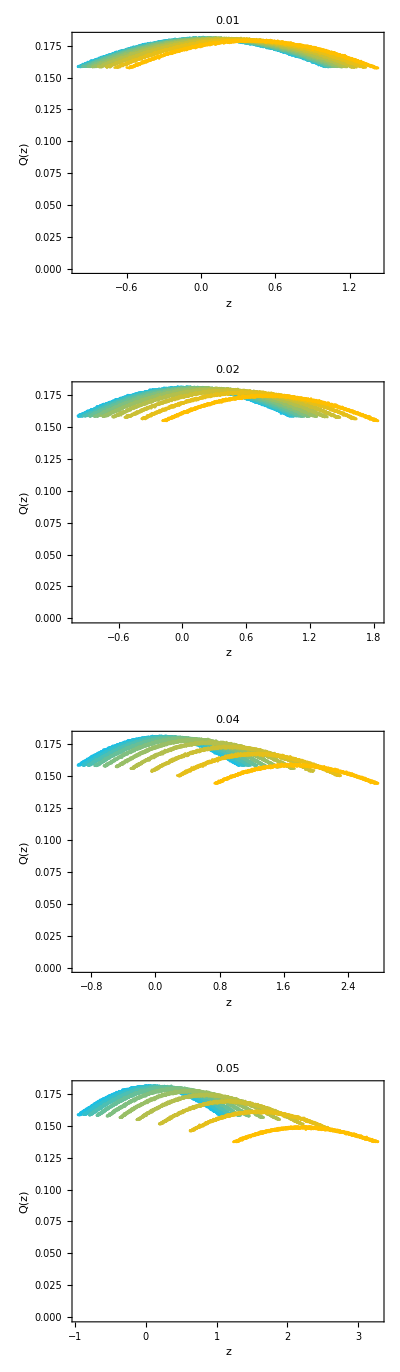

```mathematica
GraphicsColumn[tipplot]
```

#### 3D Plots

```mathematica
(*GraphicsColumn[Table[ListPlot3D[Flatten[threedfull[[i]],1]],{i,1,Length[zpushvalues]}]]*)
```

#### starting to fit gaussian to determine zmax and errors

```mathematica
startingvals = NonlinearModelFit[tip[[1]][[1]],a Exp[-(x-b)^2/(2*c^2)],{a,b,c},x][[1]][[2]];
errors = {};
zmax=Table[If[j==1,lastb=0;lasta=a/. startingvals;lastc=c /. startingvals;];fit = NonlinearModelFit[tip[[i]][[j]],a Exp[-(x-b)^2/(2*c^2)],{{a,lasta},{b,lastb},{c,lastc}},x][[1]][[2]];
Append[errors,fit["ParameterErrors"]];
lasta = a /. fit;lastb = b /. fit; lastc = c/. fit; lastb,{i,1,Length[zpushvalues]},{j,importrange}];
errors=Table[If[j==1,lastb=0;lasta=a/. startingvals;lastc=c /. startingvals;];fit = NonlinearModelFit[tip[[i]][[j]],a Exp[-(x-b)^2/(2*c^2)],{{a,lasta},{b,lastb},{c,lastc}},x];lasta = a /. fit[[1]][[2]];lastb = b /. fit[[1]][[2]]; lastc = c/. fit[[1]][[2]]; fit["ParameterConfidenceIntervals"][[2]],{i,1,Length[zpushvalues]},{j,importrange}];
bootstraperrors=Table[If[j==1,lastb=0;lasta=a/. startingvals;lastc=c /. startingvals;];fit = NonlinearModelFit[tipsubsets[[i]][[j]][[k]],a Exp[-(x-b)^2/(2*c^2)],{{a,lasta},{b,lastb},{c,lastc}},x][[1]][[2]];lasta = a /. fit;lastb = b /. fit; lastc = c/. fit; lastb,{i,1,Length[zpushvalues]},{j,importrange},{k,1,bootstrapsets}];
bootstraperrormin = Table[zmax[[i]][[j]]-Min[bootstraperrors[[i]][[j]]],{i,1,Length[zpushvalues]},{j,importrange}];
bootstraperrormax = Table[Max[bootstraperrors[[i]][[j]]]-zmax[[i]][[j]],{i,1,Length[zpushvalues]},{j,importrange}];
errorsmin = Table[zmax[[i]][[j]]-Min[errors[[i]][[j]]],{i,1,Length[zpushvalues]},{j,importrange}];
errorsmax = Table[Max[errors[[i]][[j]]]-zmax[[i]][[j]],{i,1,Length[zpushvalues]},{j,importrange}];
```

```mathematica
errors
test = NonlinearModelFit[tip[[3]][[3]],a Exp[-(x-b)^2/(2*c^2)],{{a,lasta},{b,lastb},{c,lastc}},x]
test["ParameterErrors"]
```

{{{0.0106648,0.0121185},{0.0234113,0.0249073},{0.0399532,0.0414019},{0.0618434,0.0632979},{0.0899941,0.0914713},{0.127119,0.128563},{0.172068,0.173547},{0.231717,0.233155},{0.309846,0.311351},{0.407916,0.409459}},{{0.0206189,0.0220944},{0.0464258,0.0478331},{0.0796171,0.0810842},{0.122561,0.124027},{0.178313,0.179819},{0.249689,0.251182},{0.342298,0.343825},{0.460899,0.462477},{0.61568,0.617316},{0.816851,0.818602}},{{0.041426,0.0428714},{0.0943331,0.0958223},{0.161803,0.16326},{0.24806,0.249576},{0.359463,0.360986},{0.504453,0.506031},{0.692663,0.69439},{0.940234,0.942118},{1.27302,1.2752},{1.73042,1.73282}},{{0.0521761,0.0536471},{0.117984,0.119449},{0.201703,0.203155},{0.308934,0.31046},{0.448996,0.450576},{0.629843,0.631477},{0.869017,0.870772},{1.18512,1.18712},{1.62014,1.62249},{2.23844,2.24131}}}

FittedModel[0.180189 ⅇ^(-0.130389 (-0.162531+x)^2)]

{0.0000142496,0.000371387,0.00139609}

### Calculating nu and accompanying errors

```mathematica
numain = Table[Log[2^j]/Log[zmax[[i]][[j]]/(zpushvalues[[i]])],{i,1,Length[zpushvalues]},{j,importrange}];
numin = Table[Log[2^j]/Log[(zmax[[i]][[j]]-bootstraperrormin[[i]][[j]])/(zpushvalues[[i]])],{i,1,Length[zpushvalues]},{j,importrange}];
numax = Table[Log[2^j]/Log[(zmax[[i]][[j]]+bootstraperrormax[[i]][[j]])/(zpushvalues[[i]])],{i,1,Length[zpushvalues]},{j,importrange}];
rayplot = Table[{zpushvalues[[i]],Around[zmax[[i]][[j]],{bootstraperrormin[[i]][[j]],bootstraperrormax[[i]][[j]]}]},{i,1,Length[zpushvalues]},{j,importrange}];
raymin = Transpose[Table[{zpushvalues[[i]],zmax[[i]][[j]]-bootstraperrormin[[i]][[j]]},{i,1,Length[zpushvalues]},{j,importrange}]];
raymax = Transpose[Table[{zpushvalues[[i]],zmax[[i]][[j]]+bootstraperrormax[[i]][[j]]},{i,1,Length[zpushvalues]},{j,importrange}]];
rayplotwithouterrors=Transpose[Table[{zpushvalues[[i]],zmax[[i]][[j]]},{i,1,Length[zpushvalues]},{j,importrange}]];
```

#### Plotting the critical exponents

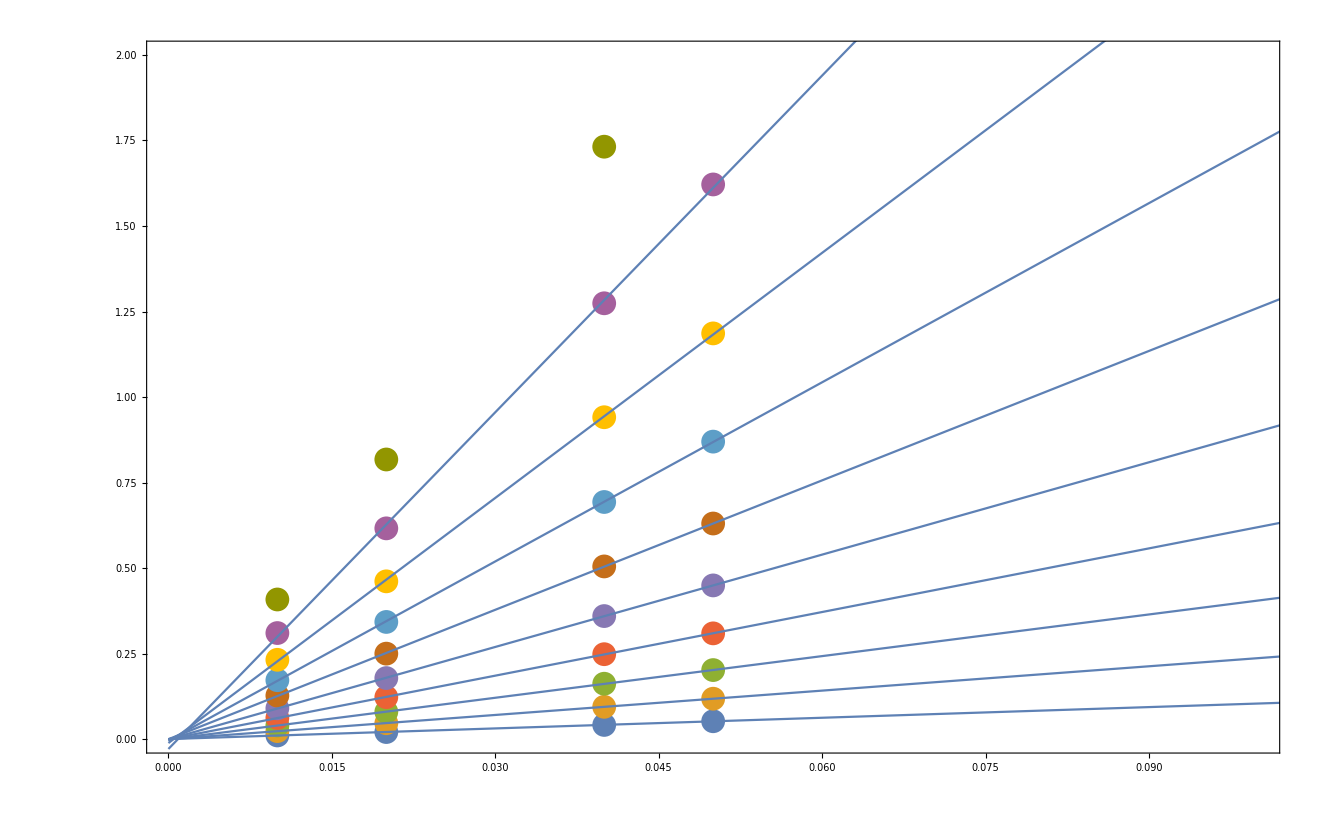

```mathematica
nuplot = Table[{2^j,Around[numain[[i]][[j]],{numain[[i]][[j]]-numin[[i]][[j]],numax[[i]][[j]]-numain[[i]][[j]]}]},{i,1,Length[zpushvalues]},{j,importrange}];
GraphicsColumn[Table[nuplot[[i]],{i,1,Length[zpushvalues]}]];
Show[ListPlot[Transpose[rayplot],PlotRange->{{0,0.1},{0,2}},Frame->True],Plot[Table[LinearModelFit[Take[rayplotwithouterrors[[i]],maxfitpointpushvalueindex],y,y][z],{i,1,maxfitpointrgstepindex}],{z,0,0.8},PlotRange->All]]
```

#### y intercepts of fitting lines without (0, 0)

```mathematica
yintercept = Table[LinearModelFit[rayplotwithouterrors[[i]],x,x]["BestFitParameters"][[1]],{i,importrange}]
```

{0.000802558,0.00015206,-0.000208074,0.000161772,0.000172723,0.000411047,-0.00356932,-0.0107011,-0.0280817,-0.0734029}

```mathematica
gradients of fitting lines without (0,0)
```

```mathematica
gradients = Table[LinearModelFit[rayplotwithouterrors[[i]],x,x]["BestFitParameters"][[2]],{i,importrange}]
```

{1.03832,2.37062,4.05684,6.19777,8.99265,12.6045,17.4464,23.8685,32.7903,45.7627}

#### plot with (0,0)

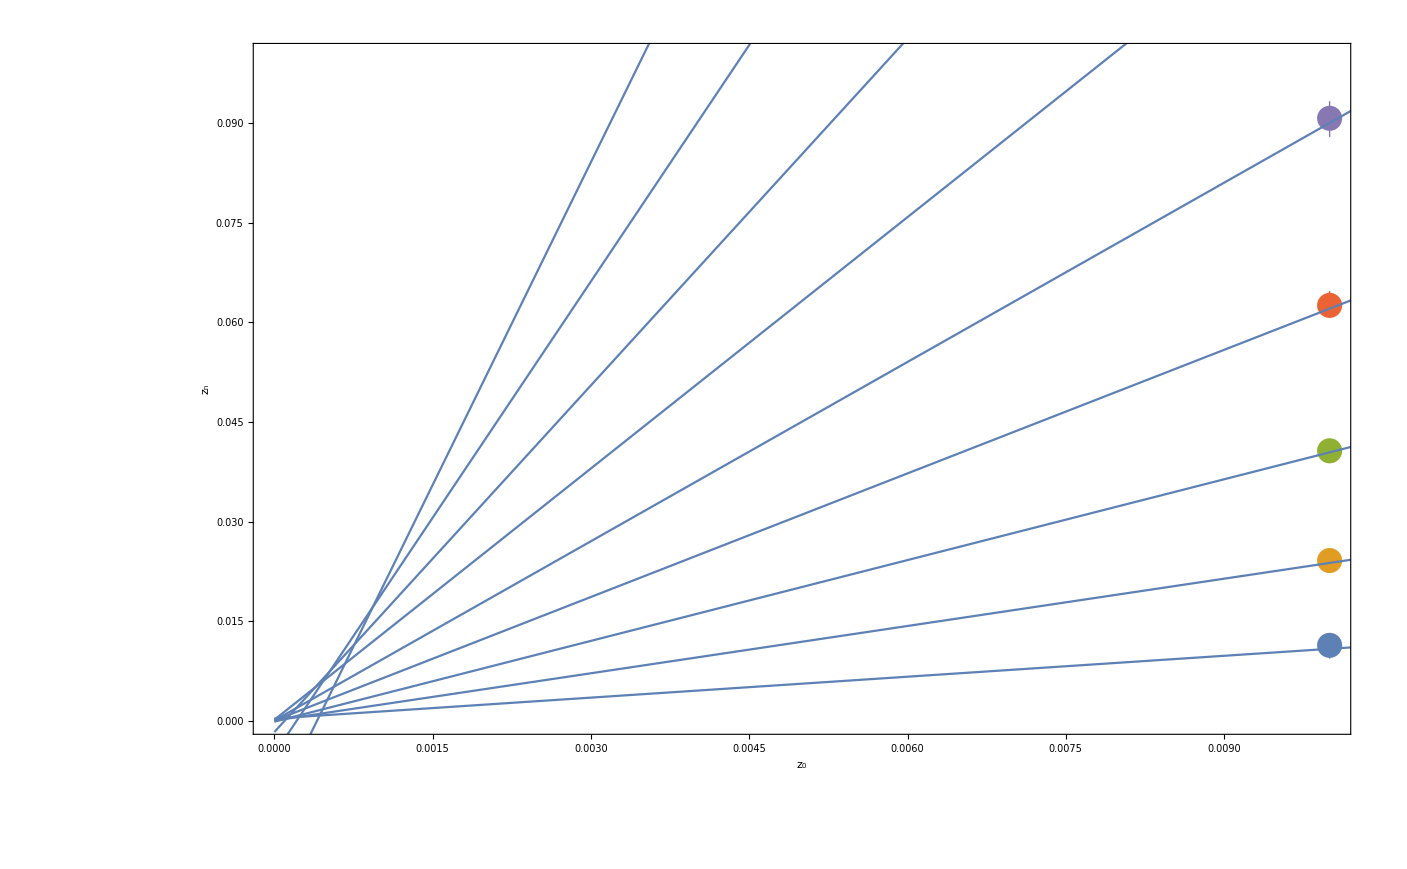

```mathematica
Show[ListPlot[Transpose[rayplot],PlotRange->{{0,0.01},{0,0.1}},Frame->True,LabelStyle->{FontSize->24}, FrameLabel->{ToExpression["z_0",TeXForm,HoldForm],ToExpression["z_n",TeXForm,HoldForm]}],Plot[Table[LinearModelFit[Prepend[Take[rayplotwithouterrors[[i]],maxfitpointpushvalueindex],{0,0}],y,y][z],{i,1,maxfitpointrgstepindex}],{z,0,0.8},PlotRange->All,Frame->True]]
```

#### y intercepts of fitting lines with (0, 0)

```mathematica
yinterceptwithzero = Table[LinearModelFit[Prepend[Take[rayplotwithouterrors[[i]],maxfitpointpushvalueindex],{0,0}],x,x]["BestFitParameters"][[1]],{i,1,maxfitpointrgstepindex}]
```

{0.000373283,0.0000707258,-0.0000967784,0.000075243,0.0000803361,0.000191185,-0.00166015,-0.00497724,-0.0130613}

#### gradients of fitting lines with (0, 0)

```mathematica
gradients = Table[LinearModelFit[Prepend[Take[rayplotwithouterrors[[i]],maxfitpointpushvalueindex],{0,0}],x,x]["BestFitParameters"][[2]],{i,1,maxfitpointrgstepindex}]
gradientsmin = Table[LinearModelFit[Prepend[Take[raymin[[i]],maxfitpointpushvalueindex],{0,0}],x,x]["BestFitParameters"][[2]],{i,1,maxfitpointrgstepindex}]
gradientsmax = Table[LinearModelFit[Prepend[Take[raymax[[i]],maxfitpointpushvalueindex],{0,0}],x,x]["BestFitParameters"][[2]],{i,1,maxfitpointrgstepindex}]

gradientserror = Table[LinearModelFit[Prepend[Take[rayplotwithouterrors[[i]],maxfitpointpushvalueindex],{0,0}],x,x]["ParameterErrors"][[2]],{i,1,maxfitpointrgstepindex}]
```

{1.04952,2.37274,4.05394,6.20003,8.99506,12.6102,17.3966,23.7192,32.3985}

{1.03239,2.32847,4.03069,6.16475,8.9776,12.5716,17.358,23.6852,32.3562}

{1.06454,2.40899,4.07339,6.21969,9.04668,12.637,17.4339,23.7385,32.4168}

{0.00943329,0.00764898,0.0117622,0.0173619,0.0168022,0.0359978,0.0569695,0.150978,0.392588}

```mathematica
LinearModelFit[Prepend[Take[rayplotwithouterrors[[3]],maxfitpointpushvalueindex],{0,0}],x,x]["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.0000967784 | 0.000356766 | -0.271266 | 0.803782
x | 4.05394 | 0.0117622 | 344.658 | 5.38634×10^-8

#### nu calculated from the gradients

{{2,14.37.3.3},{4,1.6040.040.028},{8,1.4860.0060.005},{16,1.51960.0050.0026},{32,1.57770.00140.004},{64,1.64090.00200.0014},{128,1.69870.00130.0013},{256,1.75130.00080.0005},{512,1.793590.00070.00029}}

{{2,14.3417},{4,1.60442},{8,1.48565},{16,1.5196},{32,1.57772},{64,1.64091},{128,1.69873},{256,1.75132},{512,1.79359}}

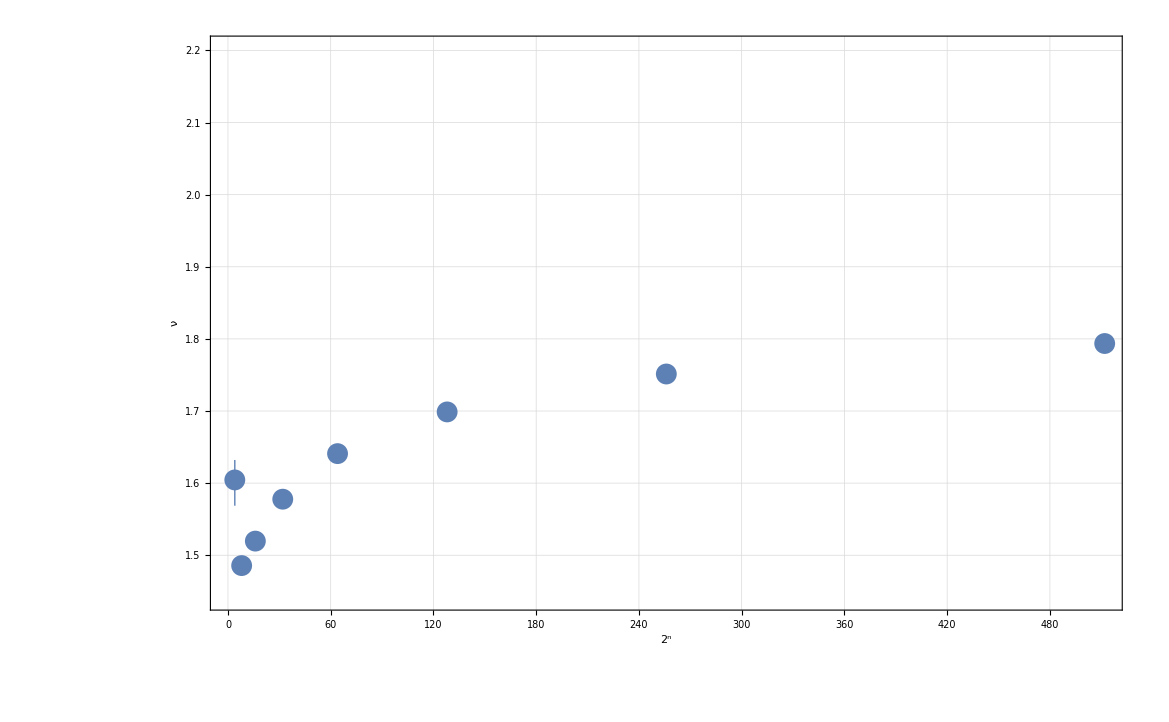

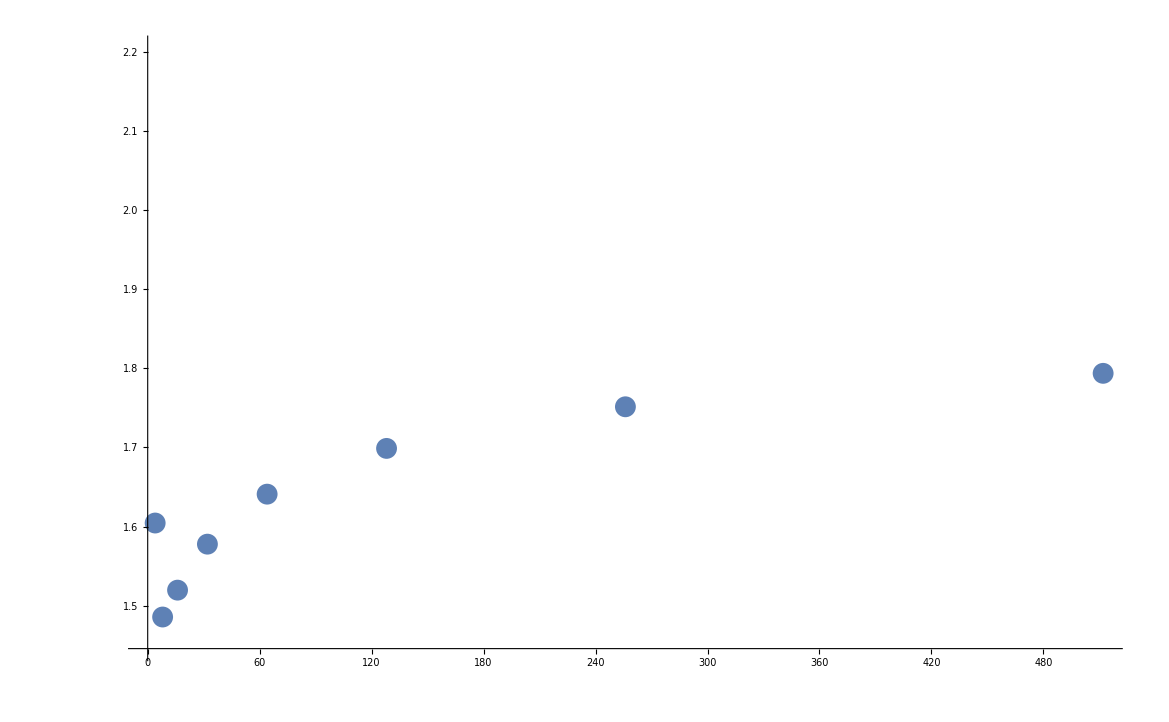

```mathematica
nufromgradientswitherror = Table[{2^j,Around[Log[2^j]/Log[gradients[[j]]],{Log[2^j]/Log[gradients[[j]]]-Log[2^j]/Log[gradientsmin[[j]]],Log[2^j]/Log[gradientsmax[[j]]]-Log[2^j]/Log[gradients[[j]]]}]},{j,1,maxfitpointrgstepindex}]
nufromgradientswithouterror = Table[{2^j,Log[2^j]/Log[gradients[[j]]]},{j,1,maxfitpointrgstepindex}]

ListPlot[nufromgradientswitherror,Frame->True,GridLines->Automatic, LabelStyle->{FontSize->24},FrameLabel->{ToExpression["2^n",TeXForm,HoldForm],ν}]
ListPlot[nufromgradientswithouterror]
```

## Saving

```mathematica
Directory[]
SetDirectory[maindir]
```

/storage/disqs/CCxD/CCGD/data

/storage/disqs/CCxD/Analysis_SS

```mathematica
nbf=NotebookFileName[]
NotebookSave[EvaluationNotebook[],"ExponentAnalysis-"<>ToString[configs]<>"-"<>ToString[matrix]<>"-"<>DateString[{"Day","-","Month","-","Year"}]<>".nb"]
NotebookSave[EvaluationNotebook[],nbf]
```

/storage/disqs/CCxD/Analysis_SS/ExponentAnalysis_SS.nb